```mathematica
hmf = ReadList[NotebookDirectory[]<>"hmf.dat",Table[Number,{3}]];
```

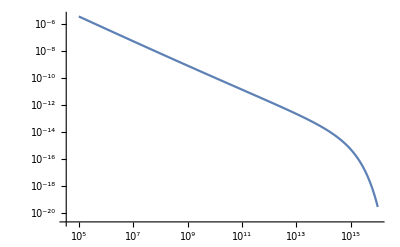

```mathematica
ListLogLogPlot[Select[hmf,#[[1]]==0.01&&#[[2]]>10^5&][[All,{2,3}]],Joined->True]
```